#### Plots of Three-Dimensional surfaces

In this exercise, we explore some of Mathematica’s capabilities for plotting multivariable functions. 

Consider a quantum mechanical problem of a particle in a two-dimensional box, i.e. quantum particle confined in two dimension between “walls” that correspond to regions of infinite potential energy, with wavefunction

	ψ_(n_1,n_2)(x,y) = (2/L) sin((n_1 πx)/L) sin((n_2 πy)/L)
	
where L is the length of the box (assumed to be the same in the x and y directions, and n_1 and n_2 are quantum numbers that are restricted to the positive integers (1, 2, 3, ...). The solution of the Schrödinger equation for this system gives the quantized energies:

		E_(n_1,n_2)=(n_1^2+n_2^2) (h^2/(8 mL^2))

where m is the mass of the particle and h is Plank’s constant. According to the Born interpretation of the wavefunction, (|ψ|)^2 is the probability density of the quantum particle, i.e., (|ψ|)^2dxdy is the probability of finding the particle within dxdy of the point (x,y).

In the following, we will plot several wavefunctions and the corresponding probability densities with x and y in units of L (i.e., we set L = 1 in the above equation) using the Plot3D command, which is analogous to the Plot command for functions of one variable:

```mathematica
psi[x_,y_]:=2Sin[n1 Pi x]Sin[n2 Pi y];
Plot3D[psi[x,y]/.{n1->2,n2->2},{x,0,1},{y,0,1},AxesLabel->{"x/L","y/L","ψ_2.2"}]
```

-Graphics3D-

```mathematica
Plot3D[(psi[x,y])^2/.{n1->2,n2->2},{x,0,1},{y,0,1},AxesLabel->{"x/L","y/L","|ψ_2.2|^2"}]
```

-Graphics3D-

```mathematica
Plot3D[psi[x,y]/.{n1->3,n2->2},{x,0,1},{y,0,1},AxesLabel->{"x/L","y/L","ψ_3.2"}]
```

-Graphics3D-

```mathematica
Plot3D[(psi[x,y])^2/.{n1->3,n2->2},{x,0,1},{y,0,1},AxesLabel->{"x/L","y/L","|ψ_3.2|^2"}]
```

-Graphics3D-

Plot3D has many options that enable you to customize your plot.

```mathematica
Plot3D[(psi[x,y])^2/.{n1->3,n2->2},{x,0,1},{y,0,1},AxesLabel->{"x/L","y/L","|ψ_3.2|^2"},PlotPoints->5]
```

-Graphics3D-

```mathematica
Plot3D[(psi[x,y])^2/.{n1->3,n2->2},{x,0,1},{y,0,1},AxesLabel->{"x/L","y/L","|ψ_3.2|^2"},PlotPoints->100]
```

-Graphics3D-

You can also change the mesh, or remove it altogether:

```mathematica
Plot3D[(psi[x,y])^2/.{n1->3,n2->2},{x,0,1},{y,0,1},AxesLabel->{"x/L","y/L","|ψ_3.2|^2"},Mesh -> 40]
```

-Graphics3D-

```mathematica
Plot3D[(psi[x,y])^2/.{n1->3,n2->2},{x,0,1},{y,0,1},AxesLabel->{"x/L","y/L","|ψ_3.2|^2"},Mesh->None]
```

-Graphics3D-

There are all sort of ways to change the coloring scheme. Here are a few examples using the ColorFunction option (read ColorSchemes in the Documentation Center for more):

```mathematica
Plot3D[(psi[x,y])^2/.{n1->3,n2->2},{x,0,1},{y,0,1},AxesLabel->{"x/L","y/L","|ψ_3.2|^2"},ColorFunction->"BlueGreenYellow"]
```

-Graphics3D-

```mathematica
Plot3D[(psi[x,y])^2/.{n1->3,n2->2},{x,0,1},{y,0,1},AxesLabel->{"x/L","y/L","|ψ_3.2|^2"},ColorFunction->"Rainbow",Mesh->None]
```

-Graphics3D-

```mathematica
Plot3D[(psi[x,y])^2/.{n1->3,n2->2},{x,0,1},{y,0,1},AxesLabel->{"x/L","y/L","|ψ_3.2|^2"},ColorFunction->"GrayTones",Mesh->None]
```

-Graphics3D-

#### Contour Plots of functions of Two Variables

A contour plot is a two-dimensional representation of a three-dimensional surface. A topographical map is an example of a contour plot. The contour lines represent “level sets”, sets of points that have the same of z (elevation in the case of a topo map). A contour plot is generated in Mathematica using the ContourPlot command:

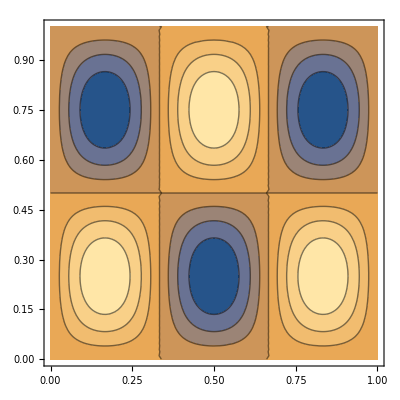

```mathematica
ContourPlot[psi[x,y]/.{n1->3,n2->2},{x,0,1},{y,0,1}]
```

You can change the number of contours and the style with which the contours are drawn:

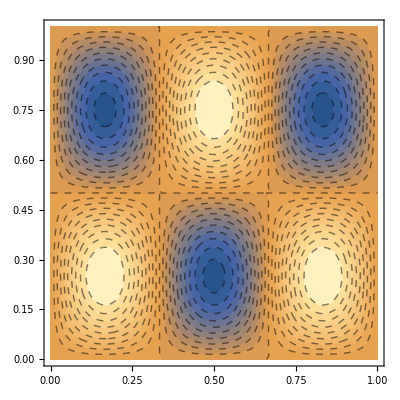

```mathematica
ContourPlot[psi[x,y]/.{n1->3,n2->2},{x,0,1},{y,0,1},Contours->20,ContourStyle->Dashed]
```

Below shows some of the options for contour plots:

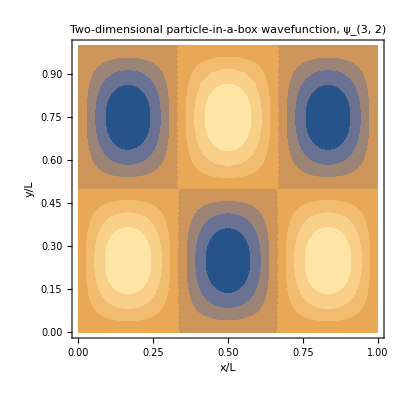

```mathematica
ContourPlot[psi[x,y]/.{n1->3,n2->2},{x,0,1},{y,0,1},FrameLabel->{"x/L","y/L"},PlotLabel->"Two-dimensional particle-in-a-box wavefunction, ψ_(3, 2)",ContourStyle->None]
```

You can show the legends:

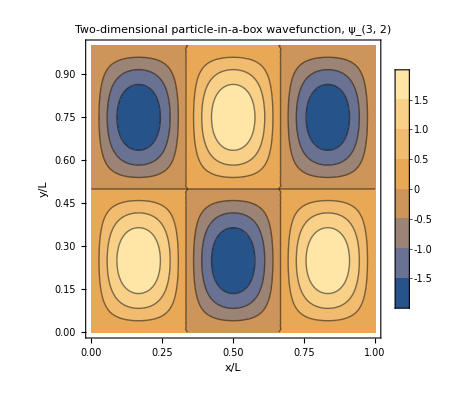

```mathematica
ContourPlot[psi[x,y]/.{n1->3,n2->2},{x,0,1},{y,0,1},FrameLabel->{"x/L","y/L"},PlotLegends->Automatic,PlotLabel->"Two-dimensional particle-in-a-box wavefunction, ψ_(3, 2)"]
```

We can also change the color scheme of the plot and legend to grayscale.

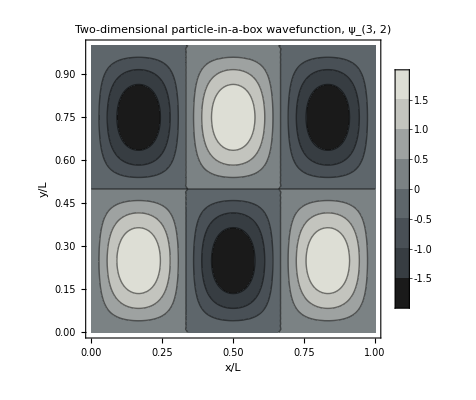

```mathematica
ContourPlot[psi[x,y]/.{n1->3,n2->2},{x,0,1},{y,0,1},FrameLabel->{"x/L","y/L"},PlotLegends->Automatic,PlotLabel->"Two-dimensional particle-in-a-box wavefunction, ψ_(3, 2)",ColorFunction->"GrayTones"]
```

#### Density Plots

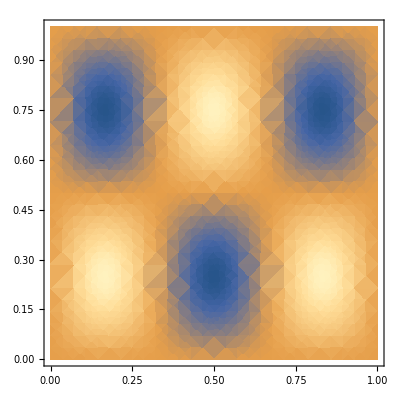

```mathematica
DensityPlot[psi[x,y]/.{n1->3,n2->2},{x,0,1},{y,0,1}]
```

The usual myriad of options for the plots are available, e.g.,

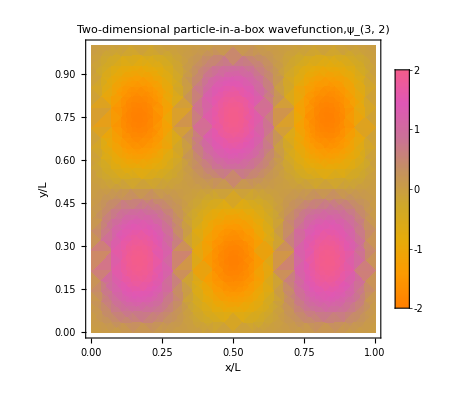

```mathematica
DensityPlot[psi[x,y]/.{n1->3,n2->2},{x,0,1},{y,0,1},FrameLabel->{"x/L","y/L"},PlotLegends->Automatic,PlotLabel->"Two-dimensional particle-in-a-box wavefunction,ψ_(3, 2)",ColorFunction->"FruitPunchColors"]
```

#### Contour Plots of Functions of Three Variables

Many functions that are of interest in chemistry are functions of three variables, and hence, are four-dimensional. Important examples include atomic and molecular wavefunctions (orbitals).  We can visualize three-dimensional contour plots of four-dimensional functions of three variables. The plots of atomic orbitals (e.g., 1s, 2p_z, 3d_(z^2), etc.) are “boundary surfaces”, where the boundary is defined by choosing a particular value (or contour), c, that defines the contour of the four-dimensional surface to be displayed, i.e., f(x,y,z) = c defines a three-dimensional contour of the four-dimensional surface described by f(x,y,z).

Mathematica has a function, ContourPlot3D, that generates a three-dimensional contour plot of a four-dimensional function. To illustrate this,  we will plot the boundary surfaces of H atom atomic orbitals and their corresponding probability densities below. The H atom wavefunctions (orbitals) are obtained by solving the Schrödinger equation for a negatively charges electron interacting with a positively charged nucleus. The standard approach to the problem is to use spherical-polar coordinates, r, θ, ϕ, where r is the distance of the electron from the nucleus and θ and ϕ are angles with respect to the Cartesian axes (x, y, and z). The general form of the solution is:

		ψ_(n,l,m_l) = R_(n.l)(r)Y_(l,m_l)(θ,ϕ)

The indices n, l, and m_l are the familiar principal, orbital angular momentum, and magnetic quantum numbers, respectively. The functions R describe the radial (distance) dependence, and the functions Y (the so-called spherical harmonics) describe the angular dependence (shape) of the wavefunction. R and Y can be expressed in terms of polynomial “special functions” that are defined in Mathematica. The functions Y are complex, and hence are not easily displayed. The orbitals that are displayed in textbooks are actually linear combinations of the complex functions that are real functions in Cartesian coordinates. In Cartesian coordinates, the orbitals have the form:
	
		f(x,y,z) = A g(x,y,z) h(r)

where A is a constant and r = r(x,y,z) = (x^2+y^2+z^2). For example, if we take r to be in units of a_0(the Bohr radius), for the 1s orbital, g(x,y,z) = 1 and h(r) = e^(-r/2); and for the 3d_(z^2)orbital, g(x,y,z) = 3z^2- r^2 and h(r) = e^(-r/3).  It is straightforward to display boundary surfaces of the orbitals (and their corresponding probability densities) in Cartesian coordinates.

```mathematica
r[x_,y_,z_]:=Sqrt[x^2 + y^2 + z^2];
f[x_,y_,z_]:=E^(-r[x,y,z]);
ContourPlot3D[f[x,y,z]==0.1,{x,-3,3},{y,-3,3},{z,-3,3},AxesLabel->{"x/a_0","y/a_0","z/a_0"},PlotLabel->"H 1s orbital"]
```

-Graphics3D-

Here is r^2 f^2, which is proportional to the electron’s probability density:

```mathematica
probdens[x_,y_,z_]:=(r[x,y,z])^2 (f[x,y,z])^2;
ContourPlot3D[probdens[x,y,z]==0.1,{x,-3,3},{y,-3,3},{z,-3,3},AxesLabel->{"x/a_0","y/a_0","z/a_0"},PlotLabel->"H 1s probability density"]
```

-Graphics3D-

Here is the 2p_z orbital. Note that one lobe has a positive amplitude, and the other has a negative amplitude, so we plot two contours, f(x,y,z) = 0.1 as a green surface and f(x,y,z) = -0.1 as a yellow surface.

```mathematica
Clear[f,probdens];
f[x_,y_,z_]:=z E^(-r[x,y,z]/2);
ContourPlot3D[{f[x,y,z]==0.1,f[x,y,z]==-0.1},{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->{"x/a_0","y/a_0","z/a_0"},PlotLabel->"H 2p_z orbital",Mesh->None,ContourStyle->{Directive[Green,Specularity[White,100]],Directive[Yellow,Specularity[White,100]]}]
```

-Graphics3D-

Here is the 2p_z probability density. Note that the probability density is everywhere positive, so we only need one surface, which is plotted here in pink:

```mathematica
probdens[x_,y_,z_]:=(r[x,y,z])^2 (f[x,y,z])^2;
ContourPlot3D[probdens[x,y,z]==0.1,{x,-15,15},{y,-15,15},{z,-15,15},AxesLabel->{"x/a_0","y/a_0","z/a_0"},PlotLabel->"H 2p_z probability density",Mesh->None,ContourStyle->Directive[Pink,Specularity[White,100]]]
```

-Graphics3D-

Here is the 3d_(z^2)orbital.

```mathematica
Clear[f];
f[x_,y_,z_]:=(3 z^2-(r[x,y,z])^2)E^(-r[x,y,z]/3);
ContourPlot3D[{f[x,y,z]==0.2,f[x,y,z]==-0.2},{x,-30,30},{y,-30,30},{z,-30,30},AxesLabel->{"x/a_0","y/a_0","z/a_0"},PlotLabel->"H 3d orbital",Mesh->None,ContourStyle->{Directive[Green,Specularity[White,100]],Directive[Yellow,Specularity[White,100]]}]
```

-Graphics3D-

Contour and density plots are also useful for visualizing projections of orbitals. For example, we can slice through the orbital in the xz plane by setting y = 0, i.e., removing y from our function definitions. Below we display the 3d_(z^2)orbital and corresponding probability density in the xz plane using ContourPlot and DensityPlot. The latter is particularly nice for depicting the “fuzziness” of orbitals and probability densities. Note that the option PlotRange ⟶ All  is used in the contour plots to keep the function from being “cut off”.

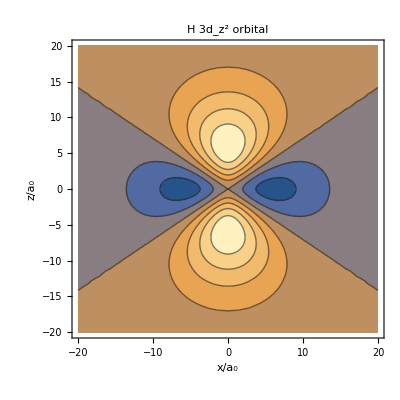

```mathematica
Clear[r,f,probdens];
r[x_,z_]:=Sqrt[x^2+z^2];
f[x_,z_]:=(3z^2-(r[x,z])^2)E^(-r[x,z]/3);
probdens[x_,z_]:=(r[x,z])^2(f[x,z])^2;
ContourPlot[f[x,z],{x,-20,20},{z,-20,20},PlotRange->All,FrameLabel->{"x/a_0","z/a_0"},PlotLabel->"H 3d_(z^2) orbital",PlotRange->All]
```

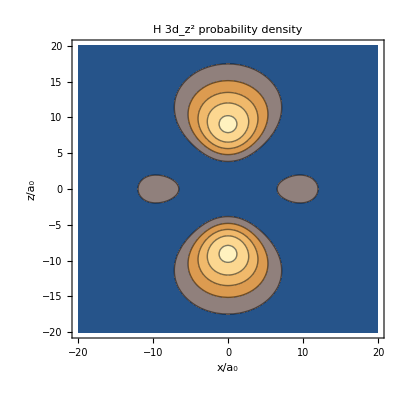

```mathematica
ContourPlot[probdens[x,z],{x,-20,20},{z,-20,20},PlotRange->All,FrameLabel->{"x/a_0","z/a_0"},PlotLabel->"H 3d_(z^2) probability density",PlotRange->All]
```

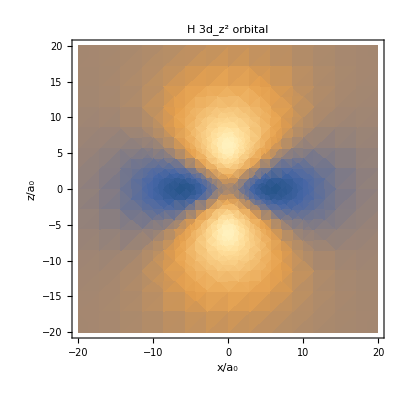

```mathematica
DensityPlot[f[x,z],{x,-20,20},{z,-20,20},PlotRange->All,FrameLabel->{"x/a_0","z/a_0"},PlotLabel->"H 3d_(z^2) orbital"]
```

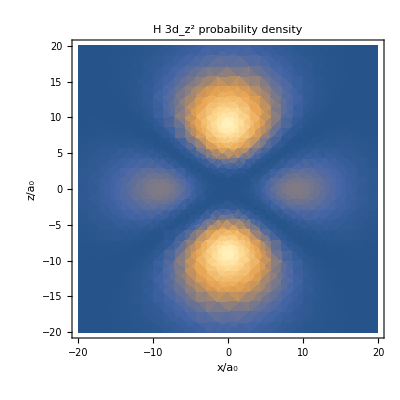

```mathematica
DensityPlot[probdens[x,z],{x,-20,20},{z,-20,20},PlotRange->All,FrameLabel->{"x/a_0","z/a_0"},PlotLabel->"H 3d_(z^2) probability density"]
```